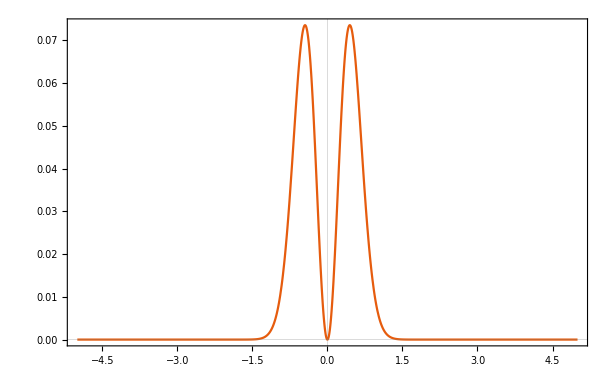

```mathematica
Plot[x^2*Exp[-5x^2], {x, -5, 5}, PlotTheme->"Scientific", PlotRange->All]
```

```mathematica
FourierTransform[x^2*Exp[-ax^2],  x, k]
```

-ⅇ^(-ax^2) √(2 π) DiracDelta''[k]

```mathematica
FourierTransform[a^2/(x^2+a^2), x, k]
```

1/2 a ⅇ^(-a k) √(π/2) ((-1+ⅇ^(2 a k)) Sign[k] (-1+Sign[Abs[Re[a]]])+2 (ⅇ^(2 a k) HeavisideTheta[-k Sign[Re[a]]]+HeavisideTheta[k Sign[Re[a]]]) Sign[Re[a]])

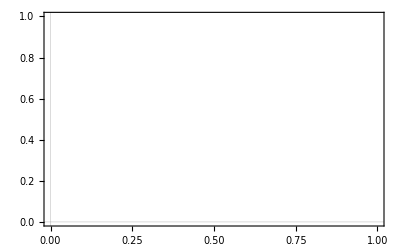

```mathematica
Plot[Sqrt[Pi/20]*Exp[-x^2/20], {x, -5, 5}, PlotTheme->"Scientific", PlotRange->All]
```